# Mathematica 计算器

## 1. 求极限，求导，积分

```mathematica
(*1. 求导*)
D[x^2+2x, x]
D[x^2+2x, y]
D[Sin[x^4], {x, 4}]//Simplify   (* 关于x的四阶导数 *)
D[y*x^2 + y^2, x, y]   (* 多元函数多次求导:先对x求导，再对得到的结果对 y 求导 *)
D[x*g[x], {x, 2}]          (* 符号函数求导 *)

(*2. 积分*)
Integrate[ⅇ^x, x]
Integrate[ⅇ^x, y]

(*3. 求极限*)
Limit[(Tan[x]-x)/(Sin[x]-x), x->0]
Limit[x^a, a->Infinity, Assumptions->-1<x<0]    (* 引入假设条件 *)
```

2+2 x

0

8 ((3-144 x^8) Cos[x^4]+2 x^4 (-51+16 x^8) Sin[x^4])

2 x

2 g'[x]+x g''[x]

ⅇ^x

ⅇ^x y

-2

0

## 多项式运算

因式分解

```mathematica
Together[1/(x-1)+ 1/(x+1)]
```

(2 x)/((-1+x) (1+x))

```mathematica
Apart[(2 x)/((-1+x) (1+x))]
```

1/(-1+x)+1/(1+x)

Collect 指定符号的相同事次的项合并在一起

```mathematica
Collect[(a+2*e)*(x^2+y^2*x^3) + b*x^2*y + c*x*y + d*x^3, x]
```

c x y+x^2 (a+2 e+b y)+x^3 (d+(a+2 e) y^2)

```mathematica
Collect[(a+2*e)*(x^2+y^2*x^3) + b*x^2*y + c*x*y + d*x^3, {x, y}]
```

c x y+x^2 (a+2 e+b y)+x^3 (d+(a+2 e) y^2)

### 简化表达式

有时你必须给出 简化 的条件

```mathematica
Simplify[Sqrt[x^2]]
Simplify[Sqrt[x^2], x>0]
```

√(x^2)

x

还有一些特殊的展开和化筒函数，

```mathematica
TrigExpand[Sin[x^2]*Cos[2*x]]

TrigReduce[Sin[x^2]^2 + Cos[x^2]^2]
```

Cos[x]^2 Sin[x^2]-Sin[x]^2 Sin[x^2]

1

## 2. 求解普通方程

```mathematica
Solve[1 + 1/2*(-3 + 2*n + n^2) == 17&&n∈Integers, {n}]
```

{{n→-7},{n→5}}

```mathematica
Solve[{2 x+ 3 y == -1, 3 x + 2 y == 1}, {x, y}]
```

{{x→1,y→-1}}

### 使用从 Solve 得到的结果(重点)

-Graphics-

使用下面的语句来获取方程的解

```mathematica
(* 如果不需要赋值变量 *)
x/.Solve[x^2 + 2*x - 1 ==0, x]
x

(* 如果要赋值变量 *)
xvar = x/.Solve[x^2 + 2*x - 1 ==0, x];

xvar
```

{-1-√2,-1+√2}

x

{-1-√2,-1+√2}

多个变量的情形

```mathematica
xyvars = {x, y}/.Solve[{2 x+ 3 y == -1, 3 x + 2 y == 1}, {x, y}];

xyvars//First
xyvars//Flatten
```

{1,-1}

{1,-1}

### 妙用列表:更加直观

```mathematica
f[x_] := x^3 - 2*x^2 - 5*x + 6;

Table[{x, f[x], f'[x], f''[x]}, {x, 1, 10}]//TableForm
```

1 | 0 | -6 | 2
2 | -4 | -1 | 8
3 | 0 | 10 | 14
4 | 18 | 27 | 20
5 | 56 | 50 | 26
6 | 120 | 79 | 32
7 | 216 | 114 | 38
8 | 350 | 155 | 44
9 | 528 | 202 | 50
10 | 756 | 255 | 56

## 3. 求解微分方程

1. 可以用前面的方法提取结果以便在其他指令中使用.
2. 有一个不同的指令 DSolveValue，可以直接从解里面提取值而不需要额外的处理，很多情况下这个函数十分适用.

### 3.1 没有初值

```mathematica
soln1 = DSolve[y'[x]-y[x]==(x+1)^3, y[x], x]
```

$Aborted

### 3.2 一个初值

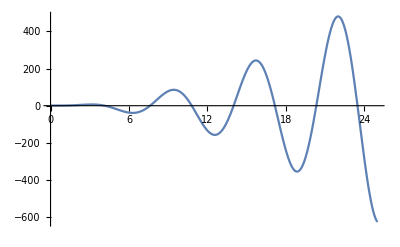

```mathematica
soln2 = DSolveValue[{y'[x] == x^2*Sin[x], y[1]==1}, y[x], x];
Plot[soln2, {x, 0, 25}]
```

### 3.3 高阶时多个初值

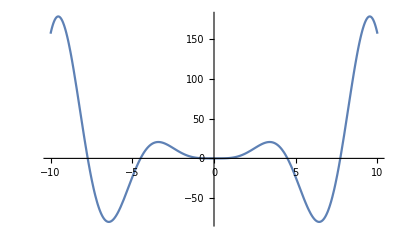

```mathematica
soln3 = DSolveValue[{y''[x] + y[x]== 8*x*Sin[x], y[0]== 0, y'[0]== 0}, y[x], x];
Plot[soln3, {x, -10, 10}]
```

### 3.4 求解初值问题

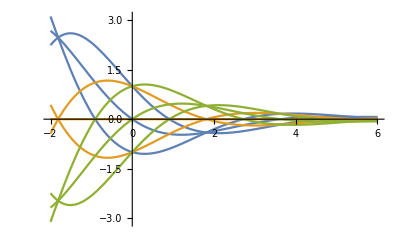

```mathematica
soln4 = DSolveValue[y''[x] + y'[x] + y[x] == 0, y[x], x];

(* 构造初值:一次性探索若干个不同的解可能很有用 *)
soln4table = Table[soln4/.{C[1] -> i,  C[2] -> j}, {i, -1, 1, 1}, {j, -1, 1, 1}];

(* 可视化各个可能解 *)
Plot[soln4table, {x, -2, 6}, PlotRange->All]
```

## 4. 矩阵运算

MMA 语言使用嵌套列表来表示矩阵。 矩阵和向量一样，矩阵可以由任意类型的表达式组成:符号、数字、字符串、图像，甚雪是它们的混合体.

### 4.1 输入矩阵

```mathematica
A = {{0, 0, 0, 1},{0,0, 1,0},{0,1,0,0},{1,0, 0, 0}}
A//MatrixForm
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

### 4.2 函数构造矩阵

无非就是使用Table 和 Array， 但是Array假定了迭代器。

注意： MMA 都是以行向量为主（前面的），一次去遍历列向量（后面的）

```mathematica
fun[x_] := Sin[x]*x;

(* 一维矩阵 *)
m1 = Array[fun, 5]
m2 = Table[fun[i], {i, 1, 5}]

(* 二维矩阵 *)
m3 = Table[i*j, {i, 1, 5}, {j, 1, 5}]//MatrixForm
```

{Sin[1],2 Sin[2],3 Sin[3],4 Sin[4],5 Sin[5]}

{Sin[1],2 Sin[2],3 Sin[3],4 Sin[4],5 Sin[5]}

(1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

RandomInteger 和 RandomReal 这样的指令可以产生多维输出，适合用来生成随机矩阵.两个指令部接受：

第一个参数作为生成随机数大小的上界和下界
第二个参数则指定了矩阵的大小.

```mathematica
RandomInteger[{1, 10}]
RandomInteger[{1, 10},  {3, 4}]//MatrixForm


RandomReal[{1, 10}]
RandomReal[{1, 10},  {3, 4}]//MatrixForm
```

10

(4 | 9 | 5 | 5
10 | 1 | 5 | 7
8 | 3 | 3 | 5)

6.7231

(6.71916 | 6.07025 | 3.83157 | 4.85623
1.94397 | 4.10466 | 6.50348 | 7.77592
5.48484 | 3.69701 | 3.00321 | 4.09742)

### 4.3 导入多维数据构建矩阵

```mathematica
mat4 = Import["http://www.handsonstart.com/RandomMatrix.csv"]//MatrixForm
```

(42 | 30 | 3 | 3 | 45 | 44 | 78 | 1 | 16 | 66
72 | 54 | 30 | 94 | 60 | 75 | 23 | 92 | 49 | 41
69 | 100 | 34 | 51 | 56 | 55 | 7 | 47 | 30 | 20
76 | 9 | 20 | 13 | 49 | 78 | 18 | 68 | 38 | 54
71 | 51 | 37 | 21 | 68 | 8 | 91 | 51 | 22 | 91
99 | 22 | 92 | 78 | 88 | 66 | 69 | 61 | 96 | 96
52 | 44 | 18 | 87 | 42 | 60 | 7 | 53 | 93 | 15
95 | 79 | 94 | 71 | 75 | 93 | 69 | 95 | 17 | 84
11 | 40 | 40 | 4 | 15 | 99 | 79 | 68 | 89 | 52
89 | 29 | 55 | 95 | 6 | 33 | 83 | 77 | 86 | 18)

### 4.4 对应，内(点)积和外积

```mathematica
vec1 = {a, b, c};
vec2 = {d, e, f};

vec1*vec2                        (* 对应相乘 *)
Dot[vec1, vec2]                  (* 内积 *)
Cross[vec1, vec2]                (* 外积 *)
Norm[vec2]                       (* 模长 *)
Normalize[{1, 2}]                (* 归一化 *)
Projection[{1, 2}, {2, 3}]       (* 前一个向量再后一个向量上的投影 *)
Orthogonalize[{{1, 2}, {2, 3}}]  (* 正交化 *)
```

{a d,b e,c f}

a d+b e+c f

{-c e+b f,c d-a f,-b d+a e}

√(Abs[d]^2+Abs[e]^2+Abs[f]^2)

{1/(√5),2/(√5)}

{16/13,24/13}

{{1/(√5),2/(√5)},{2/(√5),-1/(√5)}}

### 4.5 使用部分矩阵

-Graphics-
-Graphics-

```mathematica
mylist  = {1, 2, 3, 4, 5};
Part[mylist, 3]
mylist[[3]]
```

3

3

Part 可以和 Span 配合使用，提取一定范围内的值. Span 使用;;作为筒写形式

```mathematica
Span[2, 5]

Part[mylist, 2;;5]
Part[mylist, Span[2, 5]]

mylist[[2;;5]]
mylist[[Span[2, 5]]]
```

2;;5

{2,3,4,5}

{2,3,4,5}

{2,3,4,5}

«1 more identical outputs»

1. 提取列表的前 n 个元素是很常见的，所以有一个特殊指令 Take 可以完成这件事情.
2. 也可以把列表作为第三个参数传递给 Take 从而为其指定范围
3. 可以把 Take 用在矩阵上来提取整列或整行.
	这种指令形式的语法是给出行号或行号列表作为第二个参数，然后给出列号或列号列表作为第三个参数.可以用 All 作为筒写
	形式来要求给出全部行或全部列.

```mathematica
mtest = {{1, 2, 3}, {3, 4, 5}, {4, 5, 6}};

Take[mylist, 3]

Take[mylist, {3, 5}]

mtest//MatrixForm
Take[mtest, 2, All]//MatrixForm   (*取出前两行， 所有列*)
Take[mtest, All, 1]//MatrixForm   (*取出第一列， 所有行*)
```

{1,2,3}

{3,4,5}

(1 | 2 | 3
3 | 4 | 5
4 | 5 | 6)

(1 | 2 | 3
3 | 4 | 5)

(1
3
4)

### 4.7 选择元素

```mathematica
ls = {1, 2, 3, 4, 5};

ls2 = Select[ls, # > 3&]
```

{4,5}

## 5 模式匹配

以下为常用的示例: 本质上就是使用模式匹配把原本的数据提取出来，然后把提取出出来的数据进行操作

```mathematica
{a, b, c}/.{a->1, b->2, c->3}

{a, b, c}/.{x_, y_, z_}->{3, 4, 5}

{a, b, c}/.{x_, y_, z_}->{z, y, x}

(* 项数不定时 *)
{a, b, c}/.{x_, y_, z_}->x+y+z
{a, b, c}/.{x_, y_, z_}->{{x, x^2}, {y, y^2}, {z, z^2}, {x+y+z, x^2+y^2+z^2}}


(* 指定特定的模式 *)
3//Head
Pi//Head
{3, 4, Pi, E}/.x_Integer->x^2
```

{1,2,3}

{3,4,5}

{c,b,a}

a+b+c

{{a,a^2},{b,b^2},{c,c^2},{a+b+c,a^2+b^2+c^2}}

Integer

Symbol

{9,16,π,ⅇ}

## 6. 函数的模式匹配

```mathematica
h[x_Integer] := x^2;
h[2]
h[1.2]
```

4

h[1.2]

### 条件语句

```mathematica
Table[If[i>5, i, -i], {i, 1, 10}]
```

{-1,-2,-3,-4,-5,6,7,8,9,10}

## 5. 特征值相关

```mathematica
Eigenvectors[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}]//MatrixForm
Eigenvalues[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}]//MatrixForm
Eigensystem[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}]//MatrixForm
```

(-1 | 0 | 0 | 1
0 | -1 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

(-1
-1
1
1)

(-1 | -1 | 1 | 1
{-1,0,0,1} | {0,-1,1,0} | {1,0,0,1} | {0,1,1,0})

## 6. 公式排版

```mathematica
TeXForm[Expand[(1+7x+5y+6z)^2]]
```

49 x^2+70 x y+84 x z+14 x+25 y^2+60 y z+10 y+36 z^2+12 z+1

```mathematica
49 x^2+70 x y+84 x z+14 x+25 y^2+60 y z+10 y+36 z^2+12 z+1//TraditionalForm
```

49 x^2+70 x y+84 x z+14 x+25 y^2+60 y z+10 y+36 z^2+12 z+1

## 7. 概率论

Wolfram 语言为 Mathematica 用户提供了数量庞大的分布，可用于模拟各种各样的行为.
这些分布有单变量、多变量、连续和离散型等，还有一些用于金融等领域的专业分布，

### 7.1 单个随机变量

```mathematica
Probability[x == 3, x \[Distributed] DiscreteUniformDistribution[{1, 6}]]

dist = DiscreteUniformDistribution[{1, 6}];
Probability[x == 3, x\[Distributed]dist]
Probability[x == 3, Distribute[x, dist]]
```

1/6

1/6

Probability[x==3,x]

### 7.2 多个随机变量

```mathematica
(* 1. 求出单个概率 *)
Probability[x + y == 12, x \[Distributed] dist && y \[Distributed] dist]

(* 2. 求出所有概率,并且可视化 *)
probs = Table[Probability[x + y == res, x \[Distributed] dist && y \[Distributed] dist], {res, 2, 12, 1}];
BarChart[probs, ChartLabels->Table[i, {i, 2, 12}]]
```

1/36

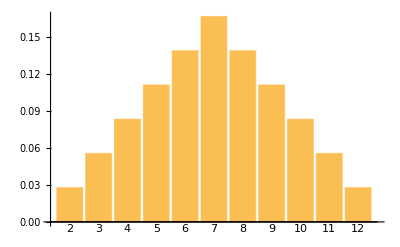

### 7.3 计算概率密度函数

```mathematica
PDF[DiscreteUniformDistribution[{1, 6}], x]
```

Piecewise[{{1/6, 1≤x≤6}, {0, True}}]

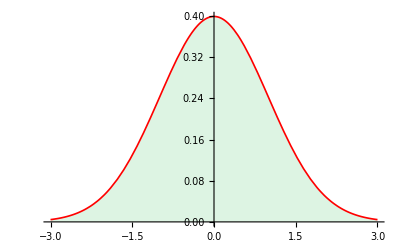

```mathematica
Plot[PDF[NormalDistribution[0, 1], x], 
	{x,-3,3}, 
	Filling -> Axis,
	FillingStyle -> Directive[Opacity[0.4], RGBColor["#ACE4B9"]],
	PlotStyle->{Thickness[0.003], Red}
]

(*这里的1， 2， 3 表示绘制的第几个函数*)
```